# Lyapunov Exponents

## Double Pendulum Example

```mathematica
ϕ10=1.57;
ϕ20=0.1;
t0=50;
```

```mathematica
m1=1.0;
m2=1.0;
l1=1.0;
l2=1.0;
g=1.0;
```

```mathematica
x1[p1_,t_]:=l1 Sin[p1[t]];
y1[p1_,t_]:=-l1 Cos[p1[t]];
x2[p1_,p2_,t_]:=x1[p1,t]+l2 Sin[p2[t]];
y2[p1_,p2_,t_]:=y1[p1,t]-l2 Cos[p2[t]];
```

```mathematica
{Φ1,Φ2}={ϕ1,ϕ2}/.NDSolve[{ϕ1''[t]==-(m2 l2)/((m1+m2)l1)ϕ2''[t]Cos[ϕ1[t]-ϕ2[t]]-(m2 l2)/((m1+m2)l1)(ϕ2'[t])^2Sin[ϕ1[t]-ϕ2[t]]-g/l1 Sin[ϕ1[t]],ϕ2''[t]==-l1/l2(ϕ1''[t]Cos[ϕ1[t]-ϕ2[t]]-(ϕ1'[t])^2Sin[ϕ1[t]-ϕ2[t]])-g/l2 Sin[ϕ2[t]],
ϕ1[0]==ϕ10,ϕ1'[0]==0,ϕ2[0]==ϕ20,ϕ2'[0]==0},
{ϕ1,ϕ2},{t,0,t0}]⟦1⟧;
{φ1,φ2}={ϕ1,ϕ2}/.NDSolve[
{ϕ1''[t]==(-m2 l2)/((m1+m2)l1)ϕ2''[t]Cos[ϕ1[t]-ϕ2[t]]-(-m2 l2)/((m1+m2)l1)(ϕ2'[t])^2Sin[ϕ1[t]-ϕ2[t]]-g/l1 Sin[ϕ1[t]],
ϕ2''[t]==-l1/l2(ϕ1''[t]Cos[ϕ1[t]-ϕ2[t]]-(ϕ1'[t])^2Sin[ϕ1[t]-ϕ2[t]])-g/l2 Sin[ϕ2[t]],
ϕ1[0]==ϕ10,ϕ1'[0]==0,ϕ2[0]==ϕ20+10^-12,ϕ2'[0]==0},
{ϕ1,ϕ2},{t,0,t0}]⟦1⟧;
```

3

Lyapunov Exponent:4.51618

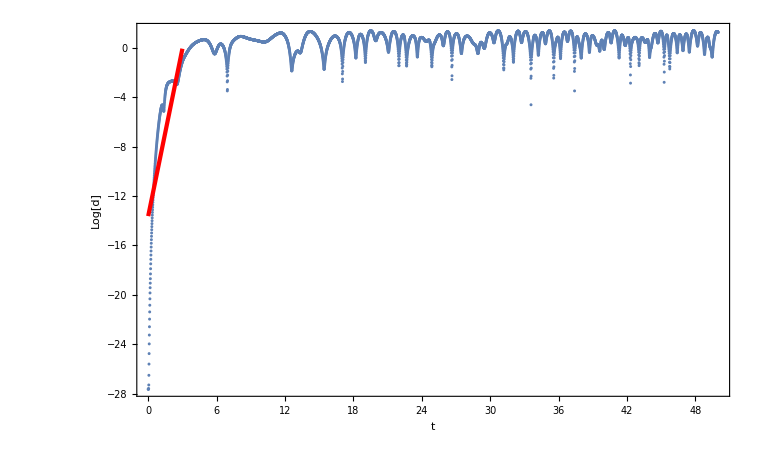

```mathematica
data=Table[{t,Log[Sqrt[(x2[Φ1,Φ2,t]-x2[φ1,φ2,t])^2+(y2[Φ1,Φ2,t]-y2[φ1,φ2,t])^2]]},{t,0,t0,0.01}];
FittingData=TakeWhile[data,#⟦2⟧<0&];
zmax=Floor[Max[FittingData[[All,1]]]]
lm=LinearModelFit[FittingData,z,z];
Print["Lyapunov Exponent:",lm["ParameterTableEntries"][[2,1]]]
Show[ListPlot[data,PlotRange->All],Plot[lm[z],{z,0,zmax},PlotStyle->Directive[Red,Thickness[0.004]]],Frame->True,FrameStyle->Thick,FrameLabel->{"t","Log[d]"},LabelStyle->Directive[Black,Bold,Larger]]
```

```mathematica
Export["/home/ben/Desktop/double_pendulum_lyapunov.png",%476,"PNG"]
```

/home/ben/Desktop/double_pendulum_lyapunov.png

```mathematica
N[Log[4]]
```

1.38629